```mathematica
(*Define constants*)
(*Rectangular coil in xy plane at z0 from origin with side lengths 2a1 and 2b1*)
r1[x_,y_,z_,a1_,b1_, z0_]:=√((a1+x)^2+(y+b1)^2+(z-z0)^2);
r2[x_,y_,z_,a1_,b1_, z0_]:=√((a1-x)^2+(y+b1)^2+(z-z0)^2);
r3[x_,y_,z_,a1_,b1_, z0_]:=√((a1-x)^2+(y-b1)^2+(z-z0)^2);
r4[x_,y_,z_,a1_,b1_, z0_]:=√((a1+x)^2+(y-b1)^2+(z-z0)^2);
d1[x_,y_,z_,a1_,b1_, z0_]:=y+b1;
d2[x_,y_,z_,a1_,b1_, z0_]:=y+b1;
d3[x_,y_,z_,a1_,b1_, z0_]:=y-b1;
d4[x_,y_,z_,a1_,b1_, z0_]:=y-b1;
c1[x_,y_,z_,a1_,b1_, z0_]:=a1+x;
c2[x_,y_,z_,a1_,b1_, z0_]:=a1-x;
c3[x_,y_,z_,a1_,b1_, z0_]:=-a1+x;
c4[x_,y_,z_,a1_,b1_, z0_]:=-a1-x;
Subscript[μ, 0]=4π 10^-7(*H/m*);
(*dimensions are in cm*)
(*Units: A*H/(m*cm), therefore need to multiply by 100x. Units are then T/A*)

(*Magnetic flux density in z direction at point (x,y,z)*)
Bz1[x_,y_,z_,a1_,b1_, z0_,N_]:=100* 10^6*(Subscript[μ, 0] N)/(4π)((-d1[x,y,z,a1,b1,z0])/(r1[x,y,z,a1,b1,z0]*(r1[x,y,z,a1,b1,z0]+c1[x,y,z,a1,b1,z0]))-c1[x,y,z,a1,b1,z0]/(r1[x,y,z,a1,b1,z0]*(r1[x,y,z,a1,b1,z0]+d1[x,y,z,a1,b1,z0]))+d2[x,y,z,a1,b1,z0]/(r2[x,y,z,a1,b1,z0]*(r2[x,y,z,a1,b1,z0]-c2[x,y,z,a1,b1,z0]))-c2[x,y,z,a1,b1,z0]/(r2[x,y,z,a1,b1,z0]*(r2[x,y,z,a1,b1,z0]+d2[x,y,z,a1,b1,z0]))+(-d3[x,y,z,a1,b1,z0])/(r3[x,y,z,a1,b1,z0]*(r3[x,y,z,a1,b1,z0]+c3[x,y,z,a1,b1,z0]))-c3[x,y,z,a1,b1,z0]/(r3[x,y,z,a1,b1,z0]*(r3[x,y,z,a1,b1,z0]+d3[x,y,z,a1,b1,z0]))+(+d4[x,y,z,a1,b1,z0])/(r4[x,y,z,a1,b1,z0]*(r4[x,y,z,a1,b1,z0]-c4[x,y,z,a1,b1,z0]))-c4[x,y,z,a1,b1,z0]/(r4[x,y,z,a1,b1,z0]*(r4[x,y,z,a1,b1,z0]+d4[x,y,z,a1,b1,z0])))
```

```mathematica
(*Helmholtz coil*)
(*in nT/mA or nT/step*)
(*Plot[Bz1[0,0,z,3.5,3.5, 1.75,12]+Bz1[0,0,z,3.5,3.5, -1.75,12],{z,-5,5}]
1000000*(Bz1[0,0,0,1.75,1.75, 0.875,12]+Bz1[0,0,0,1.75,1.75, -0.875,12])
1000000000000*(Bz1[0,0,0,1.55,1.55, 0.775,12]+Bz1[0,0,0,1.55,1.55, -0.775,12])*7.63* 10^-9*)
```

```mathematica
(*Magnetic flux density in x direction at point (x,y,z)*)
Bx1[x_,y_,z_,a1_,b1_, z0_,N_]:=100*(Subscript[μ, 0] N)/(4π)((z-z0)/(r1[x,y,z,a1,b1,z0]*(r1[x,y,z,a1,b1,z0]+d1[x,y,z,a1,b1,z0]))+(-(z-z0))/(r2[x,y,z,a1,b1,z0]*(r2[x,y,z,a1,b1,z0]+d2[x,y,z,a1,b1,z0]))+
(z-z0)/(r3[x,y,z,a1,b1,z0]*(r3[x,y,z,a1,b1,z0]+d3[x,y,z,a1,b1,z0]))+
(-(z-z0))/(r4[x,y,z,a1,b1,z0]*(r4[x,y,z,a1,b1,z0]+d4[x,y,z,a1,b1,z0])))
```

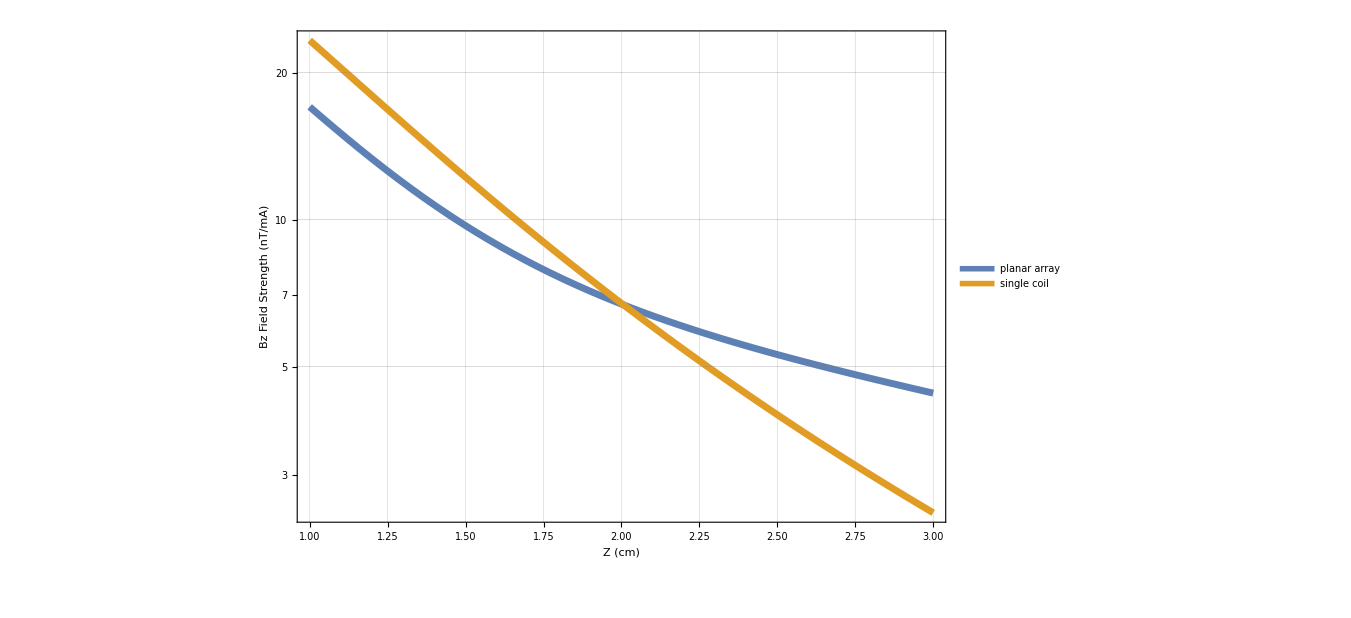

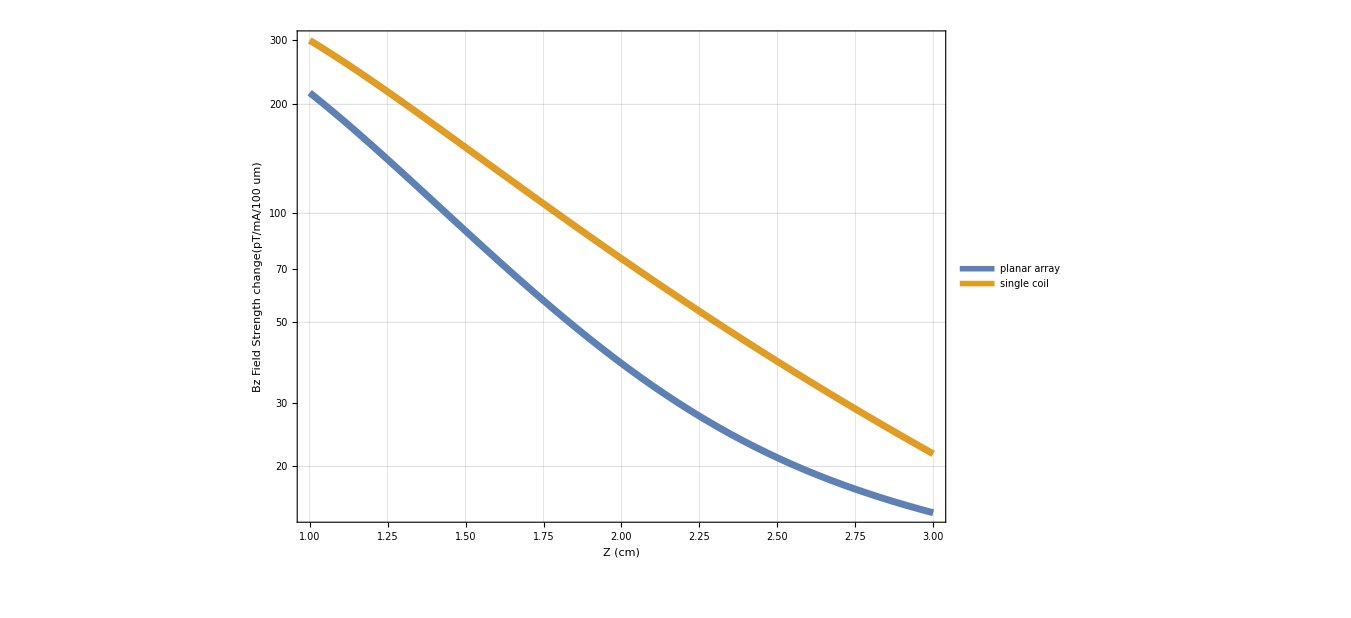

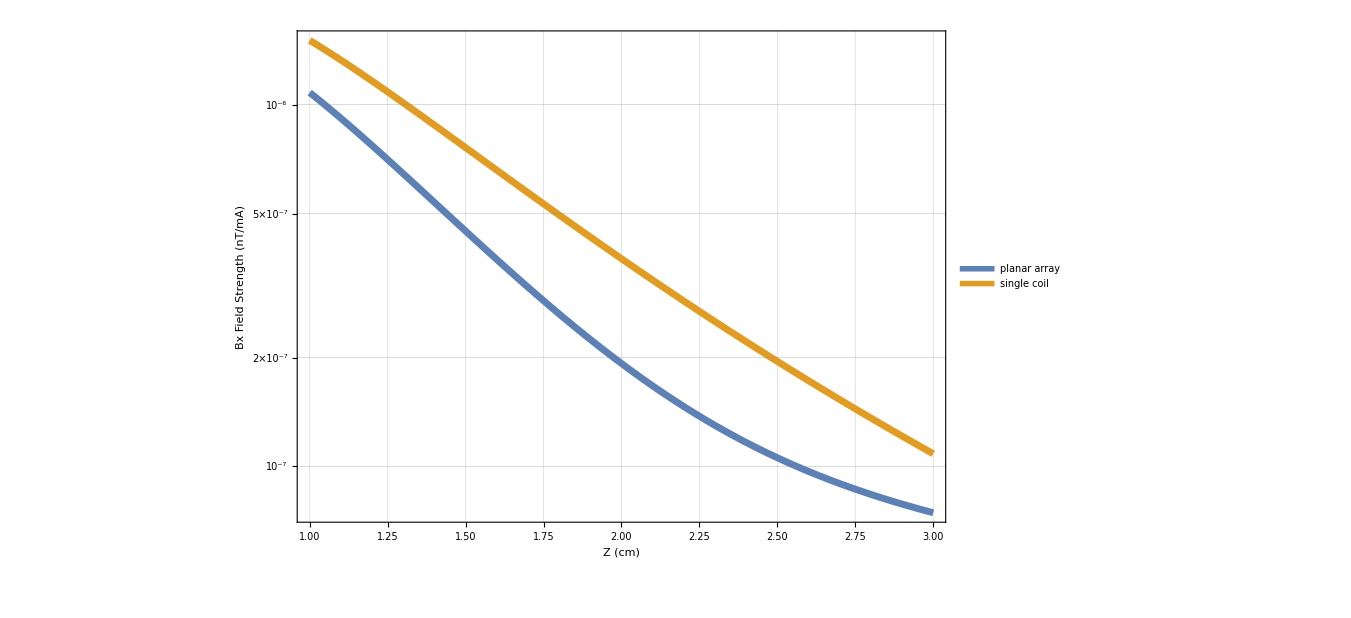

```mathematica
(*Add more coils: array of 9 coils*)
(*Planar array*)
BzParray1[x_,y_,z_,a1_,b1_, z0_,N_]:=Bz1[x,y,z,aa,bb, z0,N]+Bz1[x+spacing,y,z,aa,bb, z0,N]+Bz1[x-spacing,y,z,aa,bb, z0,N]+Bz1[x,y+spacing,z,aa,bb, z0,N]+Bz1[x+spacing,y+spacing,z,aa,bb, z0,N]+Bz1[x-spacing,y+spacing,z,aa,bb, z0,N]+Bz1[x,y-spacing,z,aa,bb, z0,N]+Bz1[x+spacing,y-spacing,z,aa,bb, z0,N]+Bz1[x-spacing,y-spacing,z,aa,bb, z0,N];
BxParray1[x_,y_,z_,a1_,b1_, z0_,N_]:=Bx1[x,y,z,aa,bb, z0,N]+Bx1[x+spacing,y,z,aa,bb, z0,N]+Bx1[x-spacing,y,z,aa,bb, z0,N]+Bx1[x,y+spacing,z,aa,bb, z0,N]+Bx1[x+spacing,y+spacing,z,aa,bb, z0,N]+Bx1[x-spacing,y+spacing,z,aa,bb, z0,N]+Bx1[x,y-spacing,z,aa,bb, z0,N]+Bx1[x+spacing,y-spacing,z,aa,bb, z0,N]+Bx1[x-spacing,y-spacing,z,aa,bb, z0,N];

LogPlot[{BzParray1[0,0,z,aa,bb, 0,1],Bz1[0,0,z,aa,bb, 0,1]},{z,1,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"planar array","single coil"},Spacings->0.15,LabelStyle->23],{0.5,0.2}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bz Field Strength (nT/mA)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
LogPlot[{1000*(BzParray1[0,0,z,aa,bb, 0,1]-BzParray1[0,0,z+0.01,aa,bb, 0,1])/1,1000*(Bz1[0,0,z,aa,bb, 0,1]-Bz1[0,0,z+0.01,aa,bb, 0,1])/1},{z,1,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"planar array","single coil"},Spacings->0.15,LabelStyle->23],{0.5,0.2}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bz Field Strength change(pT/mA/100 um)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
LogPlot[{BxParray1[0.1,0.1,z,aa,bb, 0,1],Bx1[0.1,0.1,z,aa,bb, 0,1]},{z,1,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"planar array","single coil"},Spacings->0.15,LabelStyle->23],{0.5,0.2}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bx Field Strength (nT/mA)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
```

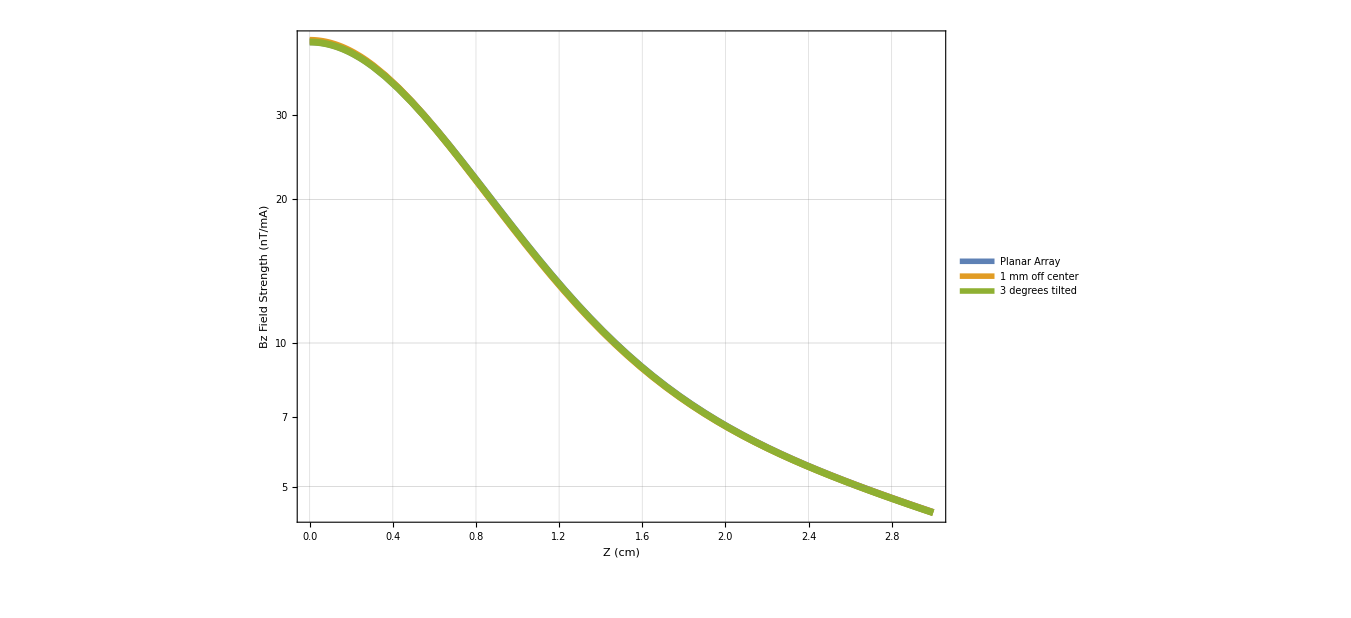

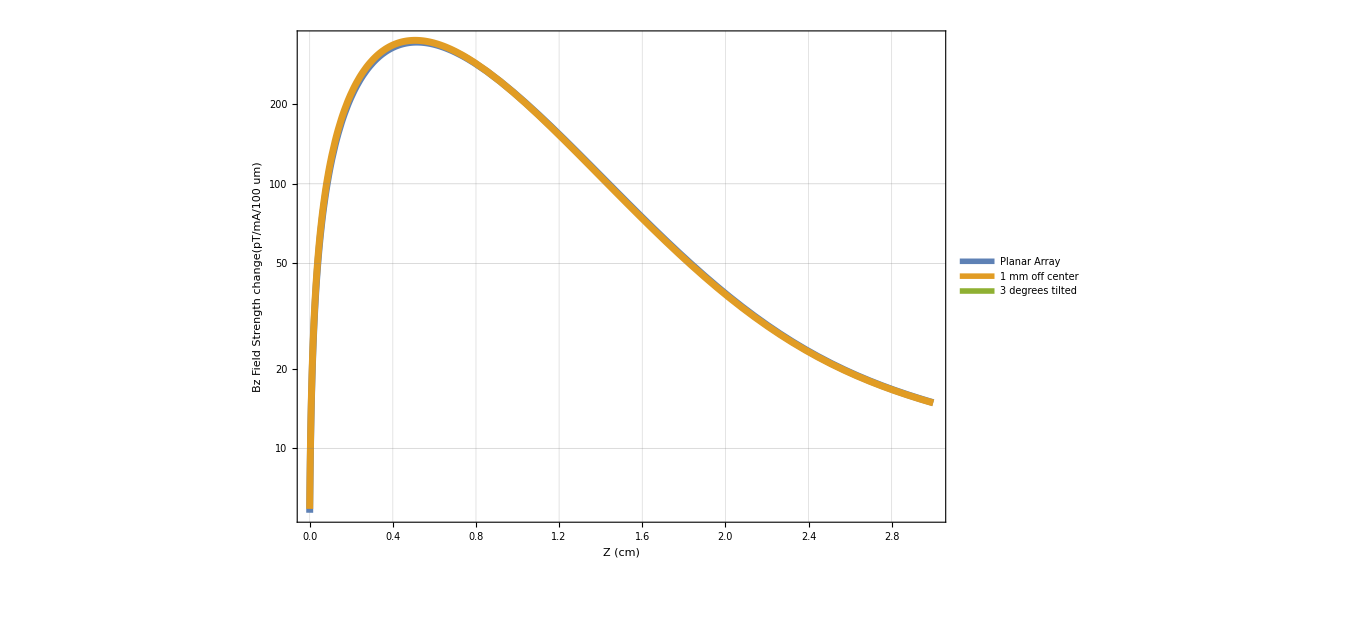

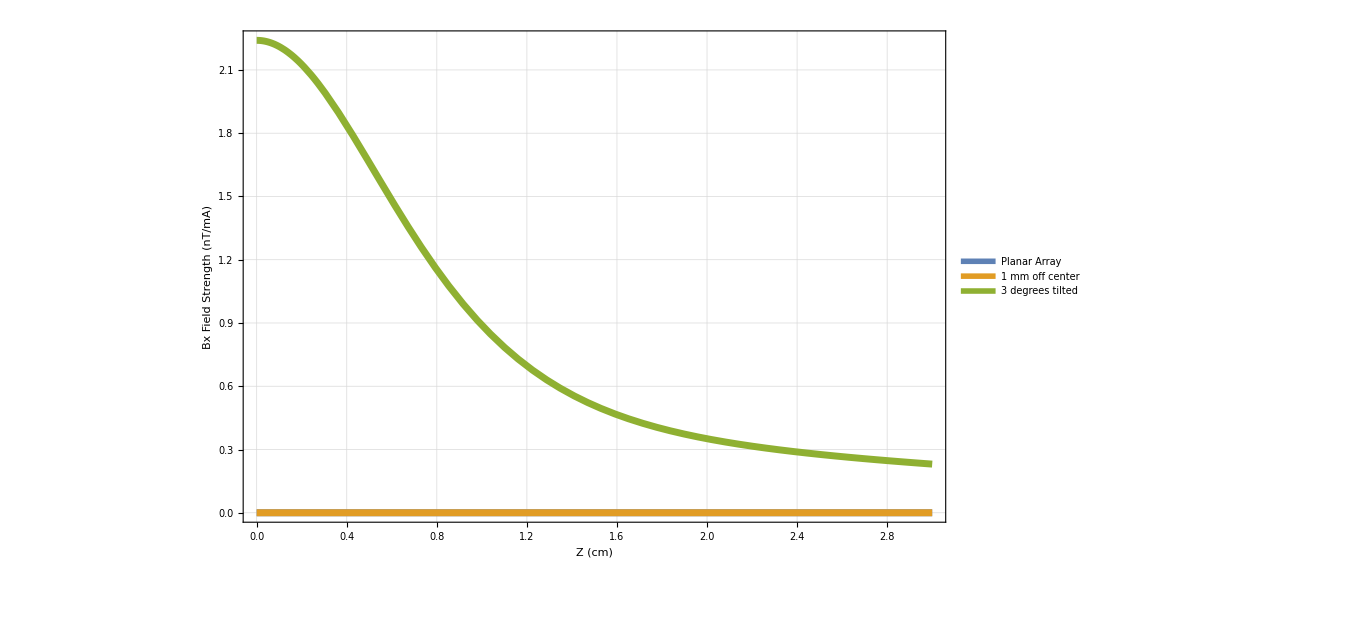

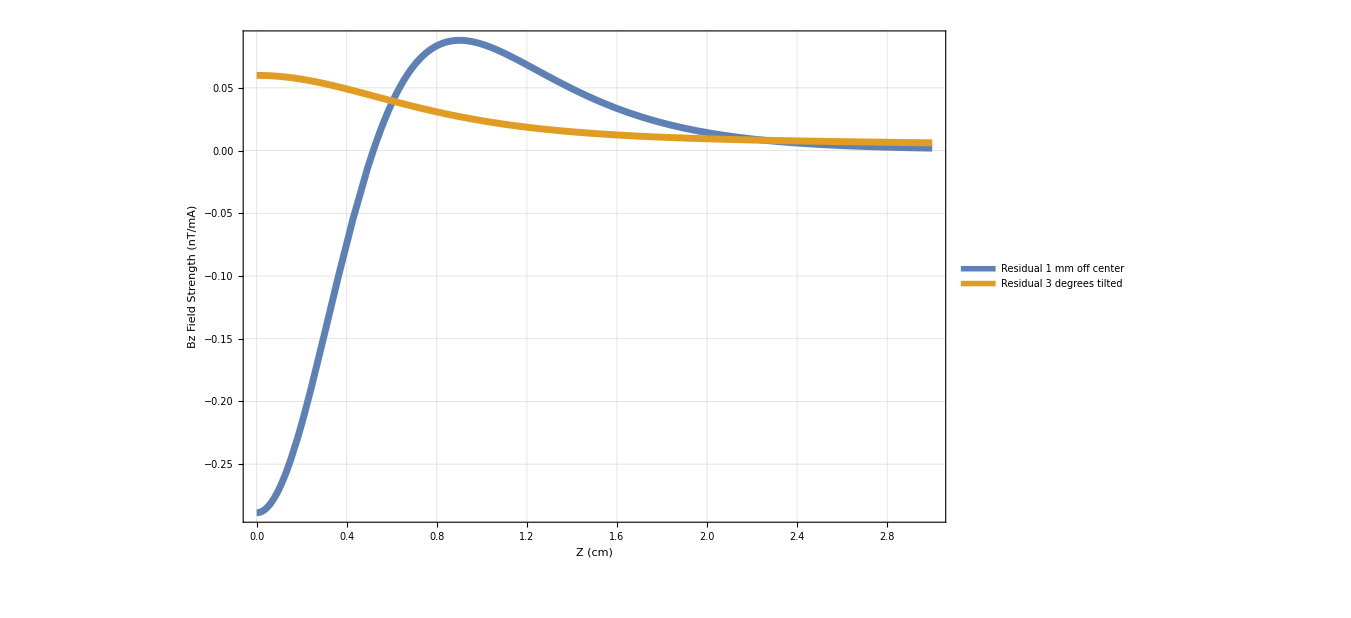

```mathematica
(*Planar array*)
LogPlot[{BzParray1[0,0,z,aa,bb, 0,1], BzParray1[0+0.1,0,z,aa,bb, 0,1], 0.9986*BzParray1[0,0,z,aa,bb, 0,1]+ 0.0523*BxParray1[0,0,z,aa,bb, 0,1]},{z,0,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"Planar Array","1 mm off center","3 degrees tilted"},Spacings->0.15,LabelStyle->23],{0.7,0.8}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bz Field Strength (nT/mA)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
LogPlot[{1000*(BzParray1[0,0,z,aa,bb, 0,1]-BzParray1[0,0,z+0.01,aa,bb, 0,1])/1,1000*(BzParray1[0.1,0,z,aa,bb, 0,1]-BzParray1[0.1,0,z+0.01,aa,bb, 0,1])/1,1000*(0.9986*BzParray1[0,0,z,aa,bb, 0,1]+ 0.0523*BxParray1[0,0,z,aa,bb, 0,1]-(0.9986*BzParray1[0,0,z,aa,bb, 0,1]+ 0.0523*BxParray1[0,0,z,aa,bb, 0,1]))/1},{z,0,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"Planar Array","1 mm off center","3 degrees tilted"},Spacings->0.15,LabelStyle->23],{0.7,0.8}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bz Field Strength change(pT/mA/100 um)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
Plot[{BxParray1[0.1,0.1,z,aa,bb, 0,1],BxParray1[0.2,0.1,z,aa,bb, 0,1],0.9986*BxParray1[0,0,z,aa,bb, 0,1]+ 0.0523*BzParray1[0,0,z,aa,bb, 0,1]},{z,0,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"Planar Array","1 mm off center","3 degrees tilted"},Spacings->0.15,LabelStyle->23],{0.7,0.8}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bx Field Strength (nT/mA)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
Plot[{BzParray1[0,0,z,aa,bb, 0,1]-BzParray1[0+0.1,0,z,aa,bb, 0,1], BzParray1[0,0,z,aa,bb, 0,1]-(0.9986*BzParray1[0,0,z,aa,bb, 0,1]+ 0.0523*BxParray1[0,0,z,aa,bb, 0,1])},{z,0,3},PlotRange->All,
PlotLegends->Placed[LineLegend[Automatic,{"Residual 1 mm off center","Residual 3 degrees tilted"},Spacings->0.15,LabelStyle->23],{0.7,0.2}],
PlotStyle->AbsoluteThickness[5],
GridLines->Automatic,Frame->True,
FrameLabel-> {"Z (cm)", "Bz Field Strength (nT/mA)"},
LabelStyle->{Directive[FontSize->30]},
ImageSize->{1000,600}]
```